## Relevant Computation for the PRL submission

## The Calligraphic F functions

```mathematica
(*the Calligraphic F's are functions used to model the time-dependence of observables related to SN1987A. A stays for Accretion Phase, C stays for Cooling Phase*)
```

```mathematica
FcalligraphicA[t_,t0_,a_]:=((1+2(t0/a)^2)/(Exp[2((t/a)^2-(t0/a)^2)]+2(t0/a)^2(t0/t)^2))^(1/2);
```

```mathematica
FcalligraphicC[t_,t0_,f_]:=((1+(t0/f))/(Exp[2((t/f)-(t0/f))]+(t0/f)(t0/t)^2))^(1/2);
```

```mathematica
FcalligraphicN[t_,t0_,n_]:=((1+2(t0/n)^2)/(Exp[2((t/n)^2-(t0/n)^2)]+2(t0/n)^2(t0/n)^2))^(1/2);
```

## Profile Likelihood of the delay times tk,ti,tb

```mathematica
profileloglikelihoodtktable={{0.0001,10.457728476264947},{0.010098999999999999,1.0641828817568353},{0.020097999999999998,0.2281152171198073},{0.030096999999999995,0.015610382363831832},{0.040096,0.018153163431350094},{0.050095,0.11577034971395506},{0.060093999999999995,0.2607390914164398},{0.070093,0.43109751065395585},{0.080092,0.6157151468946722},{0.09009099999999999,0.808512126813298},{0.10009,1.0059563007985162},{0.11008899999999999,1.2058811632889501},{0.12008799999999999,1.4068891288308123},{0.13008699999999998,1.6080453092690163},{0.140086,1.8086999914410171},{0.15008499999999997,2.0083856542042327},{0.16008399999999998,2.206755508952824},{0.17008299999999998,2.403545357765097},{0.18008199999999996,2.5985490413146977},{0.19008099999999997,2.7916015904563665},{0.20007999999999998,2.9825680918129365},{0.21007899999999996,3.1713365690341107},{0.22007799999999997,3.357812245947912},{0.23007699999999998,3.541913522160712},{0.24007599999999996,3.7235689578601523},{0.250075,3.90271502283116},{0.26007399999999997,4.079294308075987},{0.27007299999999995,4.253254021252133},{0.280072,4.424544808233577},{0.29007099999999997,4.593119629565024},{0.30006999999999995,4.758932742857382},{0.310069,4.921938649982565},{0.32006799999999996,5.082090920738892},{0.33006699999999994,5.239340899936735},{0.340066,5.3936359129208995},{0.35006499999999996,5.544917031415423},{0.36006399999999994,5.693115460282968},{0.370063,5.8381470117442404},{0.38006199999999996,5.979902586263279},{0.39006099999999994,6.118229916418727},{0.40005999999999997,6.252893093891998},{0.41005899999999995,6.384027466873988},{0.42005799999999993,6.514804517862899},{0.43005699999999997,6.645801726284844},{0.44005599999999995,6.7769887162108375},{0.4500549999999999,6.9083337889520635},{0.46005399999999996,7.039804389174947},{0.47005299999999994,7.1713665319319375},{0.4800519999999999,7.302984967715702},{0.49005099999999996,7.434622995375207},{0.50005,7.566242287178397},{0.510049,7.697804285385018},{0.520048,7.829268413230125},{0.5300469999999999,7.960592696238564},{0.5400459999999999,8.091734033213186},{0.5500449999999999,8.222647815095002},{0.560044,8.353288066657171},{0.570043,8.483607420658927},{0.580042,8.61355710443138},{0.5900409999999999,8.743087232419214},{0.6000399999999999,8.872146254209099},{0.6100389999999999,9.000681428177302},{0.620038,9.128639386301984},{0.630037,9.255964907859322},{0.6400359999999999,9.382600292832876},{0.6500349999999999,9.508490327742606},{0.6600339999999999,9.633576854830721},{0.670033,9.757801402579389},{0.680032,9.881104549047961},{0.690031,10.003426342692705},{0.7000299999999999,10.124706442006982},{0.7100289999999999,10.244884338491772},{0.7200279999999999,10.363900064433835},{0.730027,10.48169337395899},{0.740026,10.598203865028779},{0.7500249999999999,10.847930837585068},{0.7600239999999999,10.8271378951099},{0.7700229999999999,10.939467816436775},{0.7800219999999999,11.050616733995753},{0.790021,11.159489390668227},{0.80002,11.267101743554349},{0.8100189999999999,11.373080645961977},{0.8200179999999999,11.477695094895466},{0.8300169999999999,11.57978481956411},{0.8400159999999999,12.070022887471453},{0.850015,11.779363358215676},{0.860014,11.876387715178907},{0.8700129999999999,11.971535507734359},{0.8800119999999999,12.064787521161008},{0.8900109999999999,11.541004155114592},{0.9000099999999999,11.590131810852426},{0.910009,12.333058962632663},{0.9200079999999999,12.418646396054498},{0.9300069999999999,11.73718947388113},{0.9400059999999999,11.786109301714532},{0.9500049999999999,11.834999698396643},{0.9600039999999999,12.80479538539089},{0.970003,13.022315651117879},{0.9800019999999999,12.893120992508614},{0.9900009999999999,12.029956115126765},{0.9999999999999999,12.078575234306754}};
```

```mathematica
Export["profileloglikelihoodtktable.csv",profileloglikelihoodtktable]
```

profileloglikelihoodtktable.csv

```mathematica
profileloglikelihoodtitable={{0.0001,11.503200179794817},{0.015099,0.7894838218550149},{0.030098,0.08287239335544427},{0.045097000000000005,0.002213766900581504},{0.060096000000000004,0.07791020734475751},{0.07509500000000001,0.2099546217347097},{0.09009400000000001,0.36652328084949204},{0.105093,0.5349691932273686},{0.120092,0.7094560330486388},{0.135091,0.8869704648185461},{0.15009,1.065811395322953},{0.16508899999999999,1.2449454338043324},{0.180088,1.4237043055730965},{0.19508699999999998,1.6016321426555464},{0.210086,1.778403860130993},{0.22508499999999998,1.9537787520536085},{0.240084,2.127573860552957},{0.255083,2.2996503064549643},{0.270082,2.4698945683404645},{0.285081,2.638216179157155},{0.30008,2.804549106067043},{0.315079,2.968841118390685},{0.330078,3.13104467924461},{0.34507699999999997,3.2911297369874433},{0.360076,3.449078587060569},{0.375075,3.60487821412471},{0.390074,3.7585244402793023},{0.405073,3.91001908800456},{0.420072,4.059369020811516},{0.435071,4.2065899241325155},{0.45006999999999997,4.351625420594701},{0.465069,4.4945560747378295},{0.480068,4.635400160238646},{0.495067,4.77417653972077},{0.510066,4.910904205878751},{0.525065,5.045603098277525},{0.540064,5.1782935730150825},{0.555063,5.308990001676477},{0.570062,5.43771107243299},{0.5850609999999999,5.564472488434944},{0.60006,5.689290206898875},{0.615059,5.812181138562892},{0.630058,5.933163845041577},{0.645057,6.052254772496667},{0.660056,6.16947523070462},{0.675055,6.284843137526082},{0.690054,6.398379514963494},{0.705053,6.510109255693635},{0.720052,6.620060566908137},{0.735051,6.728264700963109},{0.75005,6.834756732814981},{0.765049,6.93957585686951},{0.780048,7.042765468147309},{0.795047,7.144373204655267},{0.810046,7.244450845126664},{0.825045,7.343054058779273},{0.840044,7.440242012073668},{0.855043,7.536076435598886},{0.870042,7.630621690661542},{0.885041,7.723944399825768},{0.90004,7.8161115459751045},{0.915039,7.907190302095728},{0.930038,7.997247085065396},{0.945037,8.086347063241703},{0.960036,8.174553521403027},{0.975035,8.261927348237577},{0.990034,8.348528093046923},{1.005033,8.434409703495874},{1.020032,8.519624502811553},{1.035031,8.604220575639033},{1.05003,8.688241819232246},{1.065029,8.77172977351563},{1.080028,8.854722521422957},{1.095027,8.93725485761712},{1.110026,9.019358301994714},{1.125025,9.10106213402554},{1.140024,9.182392590671725},{1.155023,9.26337346065344},{1.170022,9.344026099217444},{1.185021,9.42437070929111},{1.20002,9.504423349498268},{1.215019,9.584199430979822},{1.230018,9.663712721901561},{1.245017,9.742975154795658},{1.260016,9.821997999671737},{1.275015,9.900791095318255},{1.290014,9.979363127464012},{1.305013,10.057723014829548},{1.320012,10.135876733722569},{1.335011,10.213830057666996},{1.35001,10.291588393481504},{1.365009,10.369156542897258},{1.380008,10.446538772239194},{1.395007,10.523738874947128},{1.410006,10.60076022781493},{1.425005,10.677605690470443},{1.440004,10.754277441816555},{1.455003,10.830778274333227},{1.470002,10.907110646171247},{1.485001,10.98327650812871},{1.5,11.059277623661217}};
```

```mathematica
Export["profileloglikelihoodtitable.csv",profileloglikelihoodtitable]
```

profileloglikelihoodtitable.csv

```mathematica
profileloglikelihoodtbtable={{0.0001,8.372887941967917},{0.025099,0.30721555404568335},{0.050098000000000004,0.002806499454322875},{0.07509700000000001,0.05558809709674506},{0.100096,0.19527306325892368},{0.12509499999999998,0.36731221501628397},{0.150094,0.555152267696883},{0.175093,0.7521427461157941},{0.200092,0.9549598587226455},{0.22509099999999999,1.1616268397197587},{0.25009,1.3708018719253232},{0.275089,1.5814846248620142},{0.300088,1.7928813069519833},{0.325087,2.004336429371847},{0.350086,2.2152954967542655},{0.375085,2.4252821235810984},{0.400084,2.6338838628568055},{0.425083,2.840742917724924},{0.450082,3.045548046421345},{0.475081,3.24802874871682},{0.50008,3.4479526504462683},{0.525079,3.6451195739517175},{0.550078,3.839358909380792},{0.575077,4.030526952813261},{0.600076,4.218504418731811},{0.625075,4.403194081530273},{0.650074,4.58451922495766},{0.675073,4.762421346960593},{0.700072,4.936858457141341},{0.725071,5.107803158397644},{0.75007,5.275240227797781},{0.775069,5.439162636495894},{0.800068,5.599561659170206},{0.825067,5.755498582360644},{0.850066,5.89053184751981},{0.875065,6.030568234003397},{0.900064,6.169844353038513},{0.925063,6.308174434539296},{0.950062,8.313614524634545},{0.975061,6.626156125637237},{1.00006,6.74947308918928},{1.025059,6.862447302278099},{1.050058,6.964338519621663},{1.075057,7.055196144714955},{1.100056,7.136094957187083},{1.125055,7.208790934567332},{1.150054,7.275116925375869},{1.175053,7.336620239013712},{1.2000520000000001,7.394488984109216},{1.2250510000000001,7.449604591832951},{1.25005,7.502616654283088},{1.275049,7.554006193615578},{1.300048,7.604132360924666},{1.325047,7.653266037988828},{1.350046,7.701613513780842},{1.375045,7.749332656999172},{1.400044,7.796545139282159},{1.425043,7.843344775807452},{1.450042,7.889805005446533},{1.475041,7.935982912979512},{1.50004,7.981923021038142},{1.525039,8.027660000079493},{1.550038,8.073220624808528},{1.575037,8.11862599691591},{1.600036,8.163892198967005},{1.625035,8.209032183017257},{1.650034,8.254055753568082},{1.675033,8.298970476961529},{1.700032,8.34378217490945},{1.725031,8.38849527666531},{1.75003,8.433113060205812},{1.775029,8.477638310202792},{1.800028,8.522072906942412},{1.825027,8.566418466858863},{1.850026,8.610676136039046},{1.875025,8.654846695158597},{1.900024,8.698930911038701},{1.925023,8.742929296841794},{1.950022,8.78684221833214},{1.975021,8.83066969100338},{2.00002,8.874412291881072},{2.0250190000000003,8.918070225502163},{2.050018,8.961643308513828},{2.0750170000000003,9.00513190842662},{2.100016,9.048536265444113},{2.1250150000000003,9.091856521196917},{2.150014,9.135092782937761},{2.1750130000000003,9.178245149818167},{2.200012,9.221313396209098},{2.2250110000000003,9.26429794015354},{2.25001,9.30719890235639},{2.2750090000000003,9.3500164536527},{2.300008,9.392750579611231},{2.3250070000000003,9.435401370881152},{2.350006,9.477968917652674},{2.3750050000000003,9.520453309828667},{2.4000040000000005,9.562854637102816},{2.4250030000000002,9.60517298904955},{2.4500020000000005,9.647408455197251},{2.4750010000000002,9.689561125041791},{2.5000000000000004,9.731631088050676}};
```

```mathematica
Export["profileloglikelihoodtbtable.csv",profileloglikelihoodtbtable]
```

profileloglikelihoodtbtable.csv

## Profile likelihood of the differences of delay times tk-ti, tb-ti

### Likelihood function tk-ti

```mathematica
profilelikelihoodtkminustitable={{-2.,13.673053612742876},{-1.96,13.479862279413965},{-1.92,13.286755455738216},{-1.88,13.093738655304946},{-1.84,12.900806987545252},{-1.8,12.707762319084452},{-1.76,12.513779739716483},{-1.72,12.318758991575123},{-1.68,12.122689482982707},{-1.6400000000000001,11.925559779674359},{-1.6,11.727356175929003},{-1.56,11.528064671036304},{-1.52,11.327665121485097},{-1.48,11.126136888228984},{-1.44,10.923455547592368},{-1.4,10.719591200913214},{-1.3599999999999999,10.514500962244881},{-1.3199999999999998,10.308132998074711},{-1.28,10.100414429957425},{-1.24,9.891246382899965},{-1.2,9.680491791899442},{-1.1600000000000001,9.467958522884658},{-1.12,9.253392282963034},{-1.08,9.03645037101387},{-1.04,8.816672663395025},{-1.,8.593465209800684},{-0.96,8.366076064347851},{-0.9199999999999999,8.13358304969205},{-0.8799999999999999,7.894889201956346},{-0.8400000000000001,7.648771122333471},{-0.8,7.393950415799395},{-0.76,7.129189815846928},{-0.72,6.853389072133496},{-0.6799999999999999,6.565643650011339},{-0.6399999999999999,6.265260283885823},{-0.5999999999999999,5.951729258687067},{-0.56,5.624670455270689},{-0.52,5.283743466443013},{-0.48,4.928629302613729},{-0.43999999999999995,4.55898828771268},{-0.3999999999999999,4.174451661038347},{-0.3599999999999999,3.7745445441391894},{-0.32000000000000006,3.359258075075104},{-0.28,2.928693464510843},{-0.24,2.4833899275566864},{-0.19999999999999996,2.0245224473936787},{-0.15999999999999992,1.55432001902426},{-0.11999999999999988,1.077270740132633},{-0.08000000000000007,0.604592239621752},{-0.040000000000000036,0.17724110281210415},{0.,0.01602813849621043},{0.040000000000000036,0.509856672643366},{0.08000000000000007,1.2745653805667985},{0.1200000000000001,2.070491375980737},{0.16000000000000014,2.849335467889034},{0.20000000000000018,3.596681271167199},{0.2400000000000002,4.306021165631535},{0.28000000000000025,4.97334084620428},{0.31999999999999984,5.595261471209994},{0.3599999999999999,6.167282382972303},{0.3999999999999999,6.6954369905141675},{0.43999999999999995,7.223365011874193},{0.48,7.752460466983791},{0.52,8.280272981441783},{0.56,8.80399190914278},{0.6000000000000001,9.320432696200442},{0.6400000000000001,9.826049356345948},{0.6800000000000002,11.696441777121663},{0.7200000000000002,11.04896087138593},{0.7600000000000002,12.141013703099702},{0.8000000000000003,11.848345606655073},{0.8399999999999999,12.196331450827188},{0.8799999999999999,11.98232993679926},{0.9199999999999999,12.04874702330369},{0.96,12.79397779340377},{1.,12.439017444440708},{1.04,12.632914270301399},{1.08,12.825993889314475},{1.12,13.018261615872632},{1.1600000000000001,13.20972321159536},{1.2000000000000002,13.400384559299994},{1.2400000000000002,14.61603219937291},{1.2800000000000002,13.779330098956336},{1.3200000000000003,15.190322890258415},{1.3599999999999999,15.210788492392055},{1.4,14.341892080932155},{1.44,14.527873672334636},{1.48,14.713095647800174},{1.52,14.89756254889079},{1.56,15.081280855747877},{1.6,15.264257824200968},{1.6400000000000001,15.446497745870886},{1.6800000000000002,15.62800783742341},{1.7200000000000002,15.808793562152857},{1.7600000000000002,15.988858974463312},{1.8000000000000003,16.16820925866864},{1.8399999999999999,16.346849566654782},{1.88,16.52478448100743},{1.92,17.89966375004093},{1.96,17.018420712766556},{2.,32.13601251849872}};
```

```mathematica
Export["profilelikelihoodtkminustitable.csv",profilelikelihoodtkminustitable]
```

profilelikelihoodtkminustitable.csv

```mathematica
profilelikelihoodtkminustiinterpolation=Interpolation[profilelikelihoodtkminustitable];
```

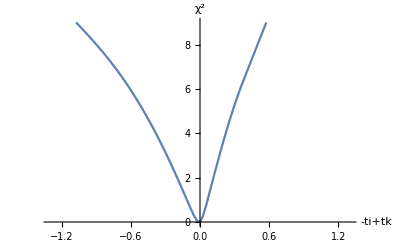

```mathematica
Plot[profilelikelihoodtkminustiinterpolation[x],{x,-1.3,1.3},PlotRange->{0,9},AxesLabel->{tk-ti,χ^2}]
```

```mathematica
NMinimize[{profilelikelihoodtkminustiinterpolation[x], -0.1<=x<=0.1},{x}]
```

{0.00790636,{x→-0.00651224}}

```mathematica
sigmaplustkminusti=Abs[(x/.FindRoot[profilelikelihoodtkminustiinterpolation[x]==1,{x,0.1}])+0.0065122382396871166]
```

0.0729599

```mathematica
sigmaminustkminusti=Abs[(x/.FindRoot[profilelikelihoodtkminustiinterpolation[x]==1,{x,-0.1}])+0.0065122382396871166]
```

0.107064

### Profile likelihood of tb-ti

```mathematica
profilelikelihoodtbminustitable={{-2.,13.754174830411557},{-1.96,13.560975477278305},{-1.92,13.367861190374356},{-1.88,13.174835562983048},{-1.84,12.981895605609111},{-1.8,12.788996969820403},{-1.76,12.595359529266489},{-1.72,12.400686606607337},{-1.68,12.204967675138732},{-1.6400000000000001,12.008191690584567},{-1.6,11.810343907918764},{-1.56,11.611412877929183},{-1.52,11.411377860561743},{-1.48,11.210219183348443},{-1.44,11.007912829986026},{-1.4,10.804430523565372},{-1.3599999999999999,10.599732724183013},{-1.3199999999999998,10.393768876807314},{-1.28,10.18647165929633},{-1.24,9.97774794859771},{-1.2,9.767471183251814},{-1.1600000000000001,9.555461081820113},{-1.12,9.341477551003209},{-1.08,9.125200580599198},{-1.04,8.906195939683755},{-1.,8.683899101218572},{-0.96,8.457591696671727},{-0.9199999999999999,8.22638490928972},{-0.8799999999999999,7.989209752154693},{-0.8400000000000001,7.74485461281995},{-0.8,7.492035151097241},{-0.76,7.229485788481611},{-0.72,6.956066059326474},{-0.6799999999999999,6.670826643713951},{-0.6399999999999999,6.37303478941584},{-0.5999999999999999,6.06214987867304},{-0.56,5.737775374412081},{-0.52,5.399559639284917},{-0.48,5.047178128199391},{-0.43999999999999995,4.680293005433725},{-0.3999999999999999,4.298539010257741},{-0.3599999999999999,3.901442378512911},{-0.32000000000000006,3.48902248330819},{-0.28,3.0613799604023484},{-0.24,2.6190361198904952},{-0.19999999999999996,2.1630934398032764},{-0.15999999999999992,1.6955643340091342},{-0.11999999999999988,1.2203140387235862},{-0.08000000000000007,0.7463611912347687},{-0.040000000000000036,0.303023581356058},{0.,0.0162974405704972},{0.040000000000000036,0.07743137327508975},{0.08000000000000007,0.32017769794396145},{0.1200000000000001,0.6168169100710088},{0.16000000000000014,0.9353494785127623},{0.20000000000000018,1.2649169213018467},{0.2400000000000002,1.6000701381395857},{0.28000000000000025,1.9372992059012972},{0.31999999999999984,2.274031353644716},{0.3599999999999999,2.6082642889998624},{0.3999999999999999,2.9384004036049873},{0.43999999999999995,3.263157494241284},{0.48,3.58151055352414},{0.52,3.8926524722200497},{0.56,4.195958947065947},{0.6000000000000001,4.490963226790541},{0.6400000000000001,4.777333368609334},{0.6800000000000002,5.0548495955507065},{0.7200000000000002,5.3233738250546025},{0.7600000000000002,5.5827684187079285},{0.8000000000000003,5.815917132279196},{0.8399999999999999,6.0409054737975225},{0.8799999999999999,6.263987119333876},{0.9199999999999999,6.4843935941342465},{0.96,6.746766464591019},{1.,6.926363168351202},{1.04,7.076363438066323},{1.08,7.200482979906894},{1.12,7.306483126135845},{1.1600000000000001,7.400981736354538},{1.2000000000000002,7.4882085672932135},{1.2400000000000002,7.570725576715745},{1.2800000000000002,7.650108746165927},{1.3200000000000003,7.727355175698733},{1.3599999999999999,7.803110240763033},{1.4,7.8777981676039985},{1.44,7.9517023086428935},{1.48,8.025012598079115},{1.52,8.09785605280473},{1.56,8.170317659056991},{1.6,8.242454536109562},{1.6400000000000001,8.314304643710216},{1.6800000000000002,8.385892850724815},{1.7200000000000002,8.457235261773008},{1.7600000000000002,8.52834262779163},{1.8000000000000003,8.599221937741959},{1.8399999999999999,8.669877498263986},{1.88,8.740312344429526},{1.92,8.810528199717623},{1.96,8.882310799349682},{2.,20.949634123283715}};
```

```mathematica
Export["profilelikelihoodtbminustitable.csv",profilelikelihoodtbminustitable]
```

profilelikelihoodtbminustitable.csv

```mathematica
profilelikelihoodtbminustiinterpolation=Interpolation[profilelikelihoodtbminustitable];
```

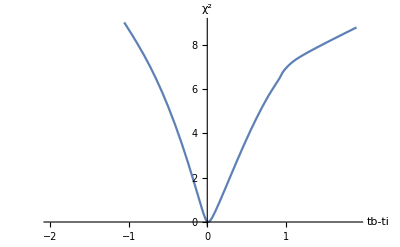

```mathematica
Plot[profilelikelihoodtbminustiinterpolation[x],{x,-2,1.90},PlotRange->{0,9},AxesLabel->{tb-ti,χ^2}]
```

```mathematica
NMinimize[{profilelikelihoodtbminustiinterpolation[x], -0.1<=x<=0.1},{x}]
```

{0.00544508,{x→0.0104346}}

```mathematica
sigmaplustbminusti=Abs[(x/.FindRoot[profilelikelihoodtbminustiinterpolation[x]==1,{x,0.1}])-0.010434634685130433]
```

0.157498

```mathematica
sigmaminustbminusti=Abs[(x/.FindRoot[profilelikelihoodtbminustiinterpolation[x]==1,{x,-0.1}])-0.010434634685130433]
```

0.112004

## Likelihood of the absolute times (point-like earth)

```mathematica
(*In this section we show the computation to obtain the estimates of the absolute time of SN1987A neutrinos*)
```

```mathematica
(*T0I is the absolute time of arrival of the first neutrino in IMB (corresponding to 0 time in the flux)*)
(*T1I is the absolute time of detection of the first neutrino. It is know with an experimental uncertainty of 50ms*)
(*T1I=T0I+ti, where ti is the delay time for IMB*)
```

```mathematica
(*likelihood T1I*)
```

```mathematica
averageT1I=0.374 (*in s*)
sigmaT1I=0.050 (*in s*)
```

0.374

0.05

```mathematica
likelihoodT1I[T1I_]:=1/((2Pi)^(1/2)*sigmaT1I)*Exp[-(T1I-averageT1I)^2/(2*(sigmaT1I)^2)];
```

```mathematica
likelihoodT1Itable=Table[likelihoodT1I[-2+i*0.06],{i,0,50}]
```

General::munfl: Exp[-1127.18] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1070.92] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1016.1] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{0.,0.,0.,0.,0.,0.,0.,0.,2.08248×10^-311,5.58699×10^-292,3.55134×10^-273,5.34837×10^-255,1.90839×10^-237,1.61335×10^-220,3.23152×10^-204,1.53356×10^-188,1.72429×10^-173,4.59341×10^-159,2.89919×10^-145,4.33545×10^-132,1.53606×10^-119,1.28943×10^-107,2.5645×10^-96,1.20844×10^-85,1.34915×10^-75,3.56873×10^-66,2.23657×10^-57,3.32099×10^-49,1.16834×10^-41,9.73835×10^-35,1.92317×10^-28,8.99844×10^-23,9.97543×10^-18,2.62007×10^-13,1.63046×10^-9,2.40393×10^-6,0.00083975,0.0695015,1.36287,6.33186,6.96985,1.81774,0.11232,0.00164436,5.70364×10^-6,4.68731×10^-9,9.12666×10^-13,4.21033×10^-17,4.60188×10^-22,1.19171×10^-27,7.31178×10^-34}

```mathematica
likelihoodT1Itable={0.,0.,0.,0.,0.,0.,0.,0.,2.0824761897445*^-311,5.586991195641828*^-292,3.5513369127139853*^-273,5.34837327450067*^-255,1.9083915749640202*^-237,1.6133523175045958*^-220,3.23152031137831*^-204,1.533559069499224*^-188,1.7242890633088785*^-173,4.593413944676112*^-159,2.8991924261962575*^-145,4.335452620737075*^-132,1.5360586331810435*^-119,1.2894279761805201*^-107,2.5644977943526172*^-96,1.208435617284467*^-85,1.3491512822084882*^-75,3.5687303131668565*^-66,2.236571339044779*^-57,3.3209912148472358*^-49,1.1683383820475864*^-41,9.73835288600423*^-35,1.9231728423457105*^-28,8.998436852646919*^-23,9.975433437792037*^-18,2.620067155387787*^-13,1.6304557505400243*^-9,2.4039285581256802*^-6,0.0008397500586323583,0.06950154755709771,1.362871322020882,6.331858154217843,6.969850255179497,1.81773958032566,0.11231967191981927,0.0016443563307257112,5.703638464568166*^-6,4.687313375586581*^-9,9.126661355676146*^-13,4.2103270183618394*^-17,4.601884006234899*^-22,1.191712384298878*^-27,7.311781140455131*^-34};
```

```mathematica
Export["likelihoodT1Itable.csv",likelihoodT1Itable]
```

likelihoodT1Itable.csv

### Likelihood of the absolute time T0I=T1I-ti

```mathematica
(*likelihood ti*)
```

```mathematica
profileloglikelihoodtiinterpolation=Interpolation[profileloglikelihoodtitable]
```

InterpolatingFunction[…]

```mathematica
chisquareti[ti_]:=profileloglikelihoodtiinterpolation[ti];
```

```mathematica
normalizationlikelihoodti=NIntegrate[Exp[(-chisquareti[ti])/2],{ti,0.0001,1.5}]
```

0.229578

```mathematica
likelihoodti[ti_]:=1/normalizationlikelihoodti Exp[(-chisquareti[ti])/2];
```

```mathematica
(*likelihood and χ^2 of T0I*)
```

```mathematica
likelihoodT1Iti[T1I_,ti_]:=likelihoodT1I[T1I]*likelihoodti[ti]; (*Note that T1I=T0I+ti*)
```

```mathematica
likelihoodT0[T0I_]:=NIntegrate[likelihoodT1Iti[T0I+ti,ti],{ti,0.0001,1.5}];
```

```mathematica
likelihoodT0table=Table[{T0I,likelihoodT0[T0I]},{T0I,-2,1,0.01}]
```

{{-2.,1.77112×10^-70},{-1.99,5.79237×10^-69},{-1.98,1.82033×10^-67},{-1.97,5.4971×10^-66},{-1.96,1.59516×10^-64},{-1.95,4.44801×10^-63},{-1.94,1.19184×10^-61},{-1.93,3.06878×10^-60},{-1.92,7.59288×10^-59},{-1.91,1.80528×10^-57},{-1.9,4.12459×10^-56},{-1.89,9.0556×10^-55},{-1.88,1.91054×10^-53},{-1.87,3.87345×10^-52},{-1.86,7.54651×10^-51},{-1.85,1.41287×10^-49},{-1.84,2.54196×10^-48},{-1.83,4.39489×10^-47},{-1.82,7.30199×10^-46},{-1.81,1.16588×10^-44},{-1.8,1.78889×10^-43},{-1.79,2.63777×10^-42},{-1.78,3.73779×10^-41},{-1.77,5.09005×10^-40},{-1.76,6.66132×10^-39},{-1.75,8.37785×10^-38},{-1.74,1.01261×10^-36},{-1.73,1.17624×10^-35},{-1.72,1.31308×10^-34},{-1.71,1.40876×10^-33},{-1.7,1.45257×10^-32},{-1.69,1.43943×10^-31},{-1.68,1.37091×10^-30},{-1.67,1.25485×10^-29},{-1.66,1.10394×10^-28},{-1.65,9.33421×10^-28},{-1.64,7.58561×10^-27},{-1.63,5.92504×10^-26},{-1.62,4.44821×10^-25},{-1.61,3.20982×10^-24},{-1.6,2.22629×10^-23},{-1.59,1.48422×10^-22},{-1.58,9.51122×10^-22},{-1.57,5.85875×10^-21},{-1.56,3.46906×10^-20},{-1.55,1.97455×10^-19},{-1.54,1.08039×10^-18},{-1.53,5.68282×10^-18},{-1.52,2.8736×10^-17},{-1.51,1.39695×10^-16},{-1.5,6.52888×10^-16},{-1.49,2.9337×10^-15},{-1.48,1.26744×10^-14},{-1.47,5.26486×10^-14},{-1.46,2.10288×10^-13},{-1.45,8.07655×10^-13},{-1.44,2.98293×10^-12},{-1.43,1.05947×10^-11},{-1.42,3.61896×10^-11},{-1.41,1.18893×10^-10},{-1.4,3.75692×10^-10},{-1.39,1.14194×10^-9},{-1.38,3.33906×10^-9},{-1.37,9.39313×10^-9},{-1.36,2.54239×10^-8},{-1.35,6.62162×10^-8},{-1.34,1.65969×10^-7},{-1.33,4.00389×10^-7},{-1.32,9.29805×10^-7},{-1.31,2.07885×10^-6},{-1.3,4.47561×10^-6},{-1.29,9.28028×10^-6},{-1.28,0.0000185373},{-1.27,0.0000356789},{-1.26,0.0000661878},{-1.25,0.000118381},{-1.24,0.000204209},{-1.23,0.000339888},{-1.22,0.000546086},{-1.21,0.000847384},{-1.2,0.00127073},{-1.19,0.00184282},{-1.18,0.00258647},{-1.17,0.00351659},{-1.16,0.00463635},{-1.15,0.0059345},{-1.14,0.00738462},{-1.13,0.00894679},{-1.12,0.0105715},{-1.11,0.0122055},{-1.1,0.013798},{-1.09,0.0153062},{-1.08,0.0166998},{-1.07,0.0179629},{-1.06,0.0190931},{-1.05,0.0200995},{-1.04,0.0209992},{-1.03,0.0218135},{-1.02,0.0225647},{-1.01,0.0232734},{-1.,0.0239572},{-0.99,0.0246301},{-0.98,0.0253026},{-0.97,0.0259821},{-0.96,0.0266738},{-0.95,0.0273811},{-0.94,0.0281061},{-0.93,0.0288507},{-0.92,0.0296158},{-0.91,0.0304024},{-0.9,0.0312114},{-0.89,0.0320434},{-0.88,0.0328994},{-0.87,0.0337801},{-0.86,0.0346863},{-0.85,0.0356188},{-0.84,0.0365786},{-0.83,0.0375667},{-0.82,0.0385838},{-0.81,0.0396312},{-0.8,0.0407098},{-0.79,0.0418208},{-0.78,0.0429653},{-0.77,0.0441446},{-0.76,0.0453599},{-0.75,0.0466128},{-0.74,0.0479044},{-0.73,0.0492365},{-0.72,0.0506106},{-0.71,0.0520284},{-0.7,0.0534917},{-0.69,0.0550023},{-0.68,0.0565624},{-0.67,0.0581739},{-0.66,0.0598392},{-0.65,0.0615606},{-0.64,0.0633406},{-0.63,0.065182},{-0.62,0.0670876},{-0.61,0.0690605},{-0.6,0.0711038},{-0.59,0.073221},{-0.58,0.0754157},{-0.57,0.0776917},{-0.56,0.0800533},{-0.55,0.0825048},{-0.54,0.0850507},{-0.53,0.0876961},{-0.52,0.0904461},{-0.51,0.0933064},{-0.5,0.0962828},{-0.49,0.0993816},{-0.48,0.102609},{-0.47,0.105973},{-0.46,0.109481},{-0.45,0.11314},{-0.44,0.116959},{-0.43,0.120947},{-0.42,0.125113},{-0.41,0.129467},{-0.4,0.13402},{-0.39,0.138783},{-0.38,0.143769},{-0.37,0.148989},{-0.36,0.154457},{-0.35,0.160187},{-0.34,0.166195},{-0.33,0.172497},{-0.32,0.179109},{-0.31,0.186049},{-0.3,0.193338},{-0.29,0.200995},{-0.28,0.209041},{-0.27,0.217502},{-0.26,0.2264},{-0.25,0.235762},{-0.24,0.245616},{-0.23,0.255993},{-0.22,0.266924},{-0.21,0.278444},{-0.2,0.290588},{-0.19,0.303396},{-0.18,0.316909},{-0.17,0.331173},{-0.16,0.346234},{-0.15,0.362145},{-0.14,0.378959},{-0.13,0.396736},{-0.12,0.415539},{-0.11,0.435435},{-0.1,0.456497},{-0.09,0.478803},{-0.08,0.502436},{-0.07,0.527485},{-0.06,0.554047},{-0.05,0.582224},{-0.04,0.612126},{-0.03,0.643873},{-0.02,0.677589},{-0.01,0.713412},{0.,0.751487},{0.01,0.79197},{0.02,0.835027},{0.03,0.880837},{0.04,0.92959},{0.05,0.98149},{0.06,1.03675},{0.07,1.09561},{0.08,1.15831},{0.09,1.2251},{0.1,1.29626},{0.11,1.37208},{0.12,1.45285},{0.13,1.53886},{0.14,1.63041},{0.15,1.7278},{0.16,1.83126},{0.17,1.94099},{0.18,2.05704},{0.19,2.17931},{0.2,2.30738},{0.21,2.44039},{0.22,2.57687},{0.23,2.7145},{0.24,2.84991},{0.25,2.97844},{0.26,3.09409},{0.27,3.18957},{0.28,3.25663},{0.29,3.28669},{0.3,3.27171},{0.31,3.20536},{0.32,3.08415},{0.33,2.90836},{0.34,2.68264},{0.35,2.41595},{0.36,2.12077},{0.37,1.81185},{0.38,1.50445},{0.39,1.21265},{0.4,0.947809},{0.41,0.71767},{0.42,0.525992},{0.43,0.372875},{0.44,0.255502},{0.45,0.169132},{0.46,0.108102},{0.47,0.0666856},{0.48,0.0396869},{0.49,0.0227787},{0.5,0.0126051},{0.51,0.00672328},{0.52,0.00345563},{0.53,0.00171117},{0.54,0.000816197},{0.55,0.000374937},{0.56,0.00016585},{0.57,0.0000706331},{0.58,0.0000289589},{0.59,0.0000114285},{0.6,4.34092×10^-6},{0.61,1.5868×10^-6},{0.62,5.58184×10^-7},{0.63,1.88934×10^-7},{0.64,6.15305×10^-8},{0.65,1.92793×10^-8},{0.66,5.81152×10^-9},{0.67,1.68523×10^-9},{0.68,4.70091×10^-10},{0.69,1.26135×10^-10},{0.7,3.25538×10^-11},{0.71,8.08099×10^-12},{0.72,1.92934×10^-12},{0.73,4.43017×10^-13},{0.74,9.78329×10^-14},{0.75,2.07774×10^-14},{0.76,4.24351×10^-15},{0.77,8.33447×10^-16},{0.78,1.57412×10^-16},{0.79,2.8589×10^-17},{0.8,4.99283×10^-18},{0.81,8.38449×10^-19},{0.82,1.35388×10^-19},{0.83,2.10207×10^-20},{0.84,3.13815×10^-21},{0.85,4.50454×10^-22},{0.86,6.21689×10^-23},{0.87,8.24962×10^-24},{0.88,1.05251×10^-24},{0.89,1.29107×10^-25},{0.9,1.52262×10^-26},{0.91,1.72644×10^-27},{0.92,1.88201×10^-28},{0.93,1.97242×10^-29},{0.94,1.98738×10^-30},{0.95,1.92513×10^-31},{0.96,1.7928×10^-32},{0.97,1.60507×10^-33},{0.98,1.38147×10^-34},{0.99,1.14307×10^-35},{1.,9.09243×10^-37}}

```mathematica
Export["likelihoodT0Itable.csv",likelihoodT0table]
```

likelihoodT0Itable.csv

```mathematica
likelihoodT0interpolation=Interpolation[likelihoodT0table]
```

InterpolatingFunction[…]

```mathematica
normalizationlikelihoodT0=NIntegrate[likelihoodT0interpolation[x],{x,-2,1}]
```

1.

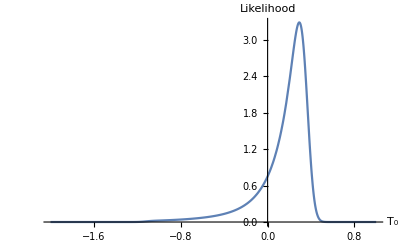

```mathematica
Plot[likelihoodT0interpolation[x],{x,-2,1},PlotRange->All,AxesLabel->{Subscript[T, 0],Likelihood}]
```

```mathematica
NMaximize[{likelihoodT0interpolation[x],0.270<=x<=0.400},{x}]
```

{3.2875,{x→0.291884}}

```mathematica
chisquareT0I[T0I_]:=-2Log[likelihoodT0interpolation[T0I]]+2Log[likelihoodT0interpolation[0.2918837503102832]];
```

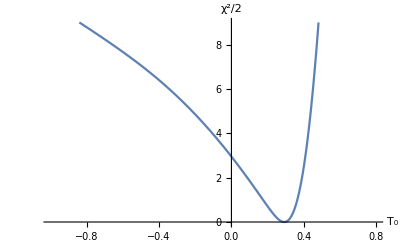

```mathematica
Plot[chisquareT0I[x],{x,-1,0.8},AxesLabel->{Subscript[T, 0],χ^2/2},PlotRange->{0,9}]
```

```mathematica
NMinimize[{chisquareT0I[x],0.2<=x<=0.4},{x}]
```

{0.,{x→0.291884}}

```mathematica
sigmaplusT0I=Abs[(x/.FindRoot[chisquareT0I[x]==1,{x,0.35}])-0.2918837503102832]
```

0.0722465

```mathematica
sigmaminusT0I=Abs[(x/.FindRoot[chisquareT0I[x]==1,{x,0.15}])-0.2918837503102832]
```

0.117251

### Profile likelihood of the absolute time T1K=T1I-ti+tk

```mathematica
(*T0KK is the absolute time of arrival of the first neutrino in KK(corresponding to 0 time in the flux). For a point-like Earth T0I=T0KK*)
(*T1KK is the absolute time of detection of the first neutrino in KK*)
(*T1KK=T0KK+tk, where tk is the delay time for IMB*)
```

```mathematica
(*likelihood ti*)
```

```mathematica
profileloglikelihoodtkinterpolation=Interpolation[profileloglikelihoodtktable]
```

InterpolatingFunction[…]

```mathematica
chisquaretk[tk_]:=profileloglikelihoodtkinterpolation[tk];
```

```mathematica
normalizationlikelihoodtk=NIntegrate[Exp[(-chisquaretk[tk])/2],{tk,0.0001,0.8}]
```

0.144248

```mathematica
likelihoodtk[tk_]:=1/normalizationlikelihoodtk Exp[(-chisquaretk[tk])/2];
```

```mathematica
(*likelihood T1KK, assuming that the three time parameters T1I, tk and ti are independent from each other*)
```

```mathematica
likelihoodT1Ititk[T1I_,ti_,tk_]:=likelihoodT1I[T1I]*likelihoodti[ti]*likelihoodtk[tk];
```

```mathematica
likelihoodT1KK[T1KK_]:=NIntegrate[likelihoodT1I[T1KK-tk+ti]*likelihoodti[ti]*likelihoodtk[tk],{tk,0.0001,0.8},{ti,0.0001,1.5}];
```

```mathematica
likelihoodT1KKtable=Table[{x,likelihoodT1KK[x]},{x,-2,2,0.01}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{{-2.,2.83431×10^-73},{-1.99,9.56591×10^-72},{-1.98,3.10325×10^-70},{-1.97,9.67655×10^-69},{-1.96,2.90029×10^-67},{-1.95,8.35568×10^-66},{-1.94,2.3139×10^-64},{-1.93,6.15933×10^-63},{-1.92,1.57598×10^-61},{-1.91,3.87616×10^-60},{-1.9,9.16407×10^-59},{-1.89,2.08264×10^-57},{-1.88,4.54972×10^-56},{-1.87,9.55436×10^-55},{-1.86,1.92872×10^-53},{-1.85,3.74277×10^-52},{-1.84,6.98195×10^-51},{-1.83,1.25206×10^-49},{-1.82,2.15844×10^-48},{-1.81,3.57708×10^-47},{-1.8,5.69898×10^-46},{-1.79,8.72867×10^-45},{-1.78,1.28525×10^-43},{-1.77,1.81937×10^-42},{-1.76,2.47603×10^-41},{-1.75,3.23965×10^-40},{-1.74,4.07522×10^-39},{-1.73,4.92859×10^-38},{-1.72,5.73088×10^-37},{-1.71,6.40697×10^-36},{-1.7,6.88691×10^-35},{-1.69,7.11778×10^-34},{-1.68,7.07328×10^-33},{-1.67,6.7587×10^-32},{-1.66,6.20982×10^-31},{-1.65,5.48629×10^-30},{-1.64,4.66093×10^-29},{-1.63,3.80776×10^-28},{-1.62,2.99145×10^-27},{-1.61,2.26007×10^-26},{-1.6,1.6421×10^-25},{-1.59,1.14744×10^-24},{-1.58,7.71128×10^-24},{-1.57,4.98428×10^-23},{-1.56,3.09866×10^-22},{-1.55,1.85292×10^-21},{-1.54,1.06578×10^-20},{-1.53,5.89694×10^-20},{-1.52,3.13871×10^-19},{-1.51,1.60717×10^-18},{-1.5,7.91741×10^-18},{-1.49,3.75263×10^-17},{-1.48,1.71138×10^-16},{-1.47,7.51×10^-16},{-1.46,3.17137×10^-15},{-1.45,1.28883×10^-14},{-1.44,5.04105×10^-14},{-1.43,1.89783×10^-13},{-1.42,6.87768×10^-13},{-1.41,2.39948×10^-12},{-1.4,8.0598×10^-12},{-1.39,2.60683×10^-11},{-1.38,8.11956×10^-11},{-1.37,2.43579×10^-10},{-1.36,7.03872×10^-10},{-1.35,1.95956×10^-9},{-1.34,5.25664×10^-9},{-1.33,1.35899×10^-8},{-1.32,3.38662×10^-8},{-1.31,8.13676×10^-8},{-1.3,1.88526×10^-7},{-1.29,4.21339×10^-7},{-1.28,9.08565×10^-7},{-1.27,1.89092×10^-6},{-1.26,3.7995×10^-6},{-1.25,7.37351×10^-6},{-1.24,0.0000138258},{-1.23,0.0000250591},{-1.22,0.0000439246},{-1.21,0.0000744993},{-1.2,0.000122335},{-1.19,0.000194619},{-1.18,0.000300166},{-1.17,0.000449179},{-1.16,0.000652723},{-1.15,0.000921924},{-1.14,0.00126695},{-1.13,0.00169588},{-1.12,0.0022137},{-1.11,0.00282151},{-1.1,0.00351614},{-1.09,0.00429032},{-1.08,0.00513324},{-1.07,0.00603158},{-1.06,0.00697071},{-1.05,0.00793596},{-1.04,0.00891373},{-1.03,0.00989229},{-1.02,0.0108623},{-1.01,0.011817},{-1.,0.0127521},{-0.99,0.0136653},{-0.98,0.0145563},{-0.97,0.0154258},{-0.96,0.0162758},{-0.95,0.0171085},{-0.94,0.0179266},{-0.93,0.018733},{-0.92,0.0195304},{-0.91,0.0203216},{-0.9,0.0211091},{-0.89,0.0218954},{-0.88,0.0226828},{-0.87,0.0234733},{-0.86,0.024269},{-0.85,0.0250718},{-0.84,0.0258835},{-0.83,0.0267056},{-0.82,0.0275398},{-0.81,0.0283876},{-0.8,0.0292504},{-0.79,0.0301296},{-0.78,0.0310266},{-0.77,0.0319426},{-0.76,0.0328791},{-0.75,0.0338373},{-0.74,0.0348184},{-0.73,0.0358238},{-0.72,0.0368547},{-0.71,0.0379124},{-0.7,0.0389983},{-0.69,0.0401136},{-0.68,0.0412599},{-0.67,0.0424384},{-0.66,0.0436506},{-0.65,0.0448981},{-0.64,0.0461825},{-0.63,0.0475053},{-0.62,0.0488684},{-0.61,0.0502736},{-0.6,0.0517227},{-0.59,0.0532178},{-0.58,0.0547611},{-0.57,0.0563546},{-0.56,0.0580009},{-0.55,0.0597023},{-0.54,0.0614615},{-0.53,0.0632814},{-0.52,0.0651649},{-0.51,0.0671151},{-0.5,0.0691353},{-0.49,0.0712291},{-0.48,0.0734001},{-0.47,0.0756524},{-0.46,0.07799},{-0.45,0.0804176},{-0.44,0.0829396},{-0.43,0.0855612},{-0.42,0.0882876},{-0.41,0.0911245},{-0.4,0.0940776},{-0.39,0.0971534},{-0.38,0.100358},{-0.37,0.1037},{-0.36,0.107185},{-0.35,0.110822},{-0.34,0.114619},{-0.33,0.118585},{-0.32,0.122729},{-0.31,0.127063},{-0.3,0.131595},{-0.29,0.136338},{-0.28,0.141304},{-0.27,0.146506},{-0.26,0.151956},{-0.25,0.157671},{-0.24,0.163664},{-0.23,0.169952},{-0.22,0.176553},{-0.21,0.183485},{-0.2,0.190768},{-0.19,0.198422},{-0.18,0.20647},{-0.17,0.214936},{-0.16,0.223844},{-0.15,0.233223},{-0.14,0.2431},{-0.13,0.253507},{-0.12,0.264476},{-0.11,0.276044},{-0.1,0.288246},{-0.09,0.301125},{-0.08,0.314723},{-0.07,0.329085},{-0.06,0.344263},{-0.05,0.360308},{-0.04,0.377278},{-0.03,0.395234},{-0.02,0.41424},{-0.01,0.434367},{0.,0.455689},{0.01,0.478287},{0.02,0.502248},{0.03,0.527662},{0.04,0.554629},{0.05,0.583255},{0.06,0.613653},{0.07,0.645944},{0.08,0.680258},{0.09,0.716733},{0.1,0.755516},{0.11,0.796767},{0.12,0.84065},{0.13,0.887344},{0.14,0.937037},{0.15,0.989924},{0.16,1.04621},{0.17,1.10611},{0.18,1.16983},{0.19,1.23757},{0.2,1.30953},{0.21,1.38587},{0.22,1.46667},{0.23,1.55193},{0.24,1.64152},{0.25,1.73506},{0.26,1.83192},{0.27,1.93109},{0.28,2.0311},{0.29,2.12999},{0.3,2.22526},{0.31,2.3139},{0.32,2.39256},{0.33,2.45767},{0.34,2.50576},{0.35,2.53375},{0.36,2.5393},{0.37,2.52106},{0.38,2.47886},{0.39,2.41378},{0.4,2.32809},{0.41,2.22498},{0.42,2.10831},{0.43,1.98224},{0.44,1.85087},{0.45,1.71798},{0.46,1.58678},{0.47,1.45986},{0.48,1.3391},{0.49,1.22571},{0.5,1.12039},{0.51,1.02336},{0.52,0.934535},{0.53,0.853578},{0.54,0.780027},{0.55,0.713339},{0.56,0.652945},{0.57,0.598279},{0.58,0.548802},{0.59,0.504006},{0.6,0.463427},{0.61,0.426639},{0.62,0.393258},{0.63,0.362936},{0.64,0.335362},{0.65,0.310255},{0.66,0.287364},{0.67,0.266463},{0.68,0.247351},{0.69,0.229847},{0.7,0.213788},{0.71,0.199029},{0.72,0.18544},{0.73,0.172905},{0.74,0.161321},{0.75,0.150595},{0.76,0.140647},{0.77,0.131404},{0.78,0.122802},{0.79,0.114785},{0.8,0.107303},{0.81,0.100314},{0.82,0.093778},{0.83,0.0876612},{0.84,0.0819326},{0.85,0.0765647},{0.86,0.071532},{0.87,0.0668115},{0.88,0.0623817},{0.89,0.0582226},{0.9,0.0543156},{0.91,0.0506433},{0.92,0.0471892},{0.93,0.0439377},{0.94,0.0408742},{0.95,0.0379849},{0.96,0.0352566},{0.97,0.0326772},{0.98,0.030235},{0.99,0.0279192},{1.,0.0257197},{1.01,0.0236272},{1.02,0.0216332},{1.03,0.0197304},{1.04,0.0179126},{1.05,0.0161749},{1.06,0.0145139},{1.07,0.0129283},{1.08,0.0114185},{1.09,0.00998696},{1.1,0.00863817},{1.11,0.00737798},{1.12,0.00621323},{1.13,0.00515088},{1.14,0.00419702},{1.15,0.00335593},{1.16,0.00262922},{1.17,0.00201529},{1.18,0.00150913},{1.19,0.00110258},{1.2,0.000784955},{1.21,0.000543906},{1.22,0.000366421},{1.23,0.000239766},{1.24,0.000152249},{1.25,0.0000937408},{1.26,0.0000559224},{1.27,0.0000323024},{1.28,0.0000180557},{1.29,9.76077×10^-6},{1.3,5.10071×10^-6},{1.31,2.57548×10^-6},{1.32,1.25601×10^-6},{1.33,5.91393×10^-7},{1.34,2.68758×10^-7},{1.35,1.17848×10^-7},{1.36,4.98468×10^-8},{1.37,2.03329×10^-8},{1.38,7.99674×10^-9},{1.39,3.0317×10^-9},{1.4,1.10774×10^-9},{1.41,3.90029×10^-10},{1.42,1.3231×10^-10},{1.43,4.32374×10^-11},{1.44,1.36096×10^-11},{1.45,4.12567×10^-12},{1.46,1.20436×10^-12},{1.47,3.38526×10^-13},{1.48,9.16124×10^-14},{1.49,2.38675×10^-14},{1.5,5.98566×10^-15},{1.51,1.4449×10^-15},{1.52,3.35704×10^-16},{1.53,7.50644×10^-17},{1.54,1.61527×10^-17},{1.55,3.34477×10^-18},{1.56,6.66459×10^-19},{1.57,1.27774×10^-19},{1.58,2.35699×10^-20},{1.59,4.18306×10^-21},{1.6,7.14226×10^-22},{1.61,1.17318×10^-22},{1.62,1.85382×10^-23},{1.63,2.8179×10^-24},{1.64,4.12027×10^-25},{1.65,5.79501×10^-26},{1.66,7.83966×10^-27},{1.67,1.0201×10^-27},{1.68,1.27667×10^-28},{1.69,1.53673×10^-29},{1.7,1.77903×10^-30},{1.71,1.98074×10^-31},{1.72,2.1209×10^-32},{1.73,2.18401×10^-33},{1.74,2.16281×10^-34},{1.75,2.05971×10^-35},{1.76,1.88628×10^-36},{1.77,1.66117×10^-37},{1.78,1.40676×10^-38},{1.79,1.14556×10^-39},{1.8,8.9701×10^-41},{1.81,6.75393×10^-42},{1.82,4.88975×10^-43},{1.83,3.40394×10^-44},{1.84,2.27843×10^-45},{1.85,1.46636×10^-46},{1.86,9.07392×10^-48},{1.87,5.39871×10^-49},{1.88,3.08831×10^-50},{1.89,1.69856×10^-51},{1.9,8.98192×10^-53},{1.91,4.56643×10^-54},{1.92,2.23203×10^-55},{1.93,1.0489×10^-56},{1.94,4.73889×10^-58},{1.95,2.05836×10^-59},{1.96,8.59532×10^-61},{1.97,3.45062×10^-62},{1.98,1.33175×10^-63},{1.99,4.94118×10^-65},{2.,1.76247×10^-66}}

```mathematica
Export["likelihoodT1KKtable.csv",likelihoodT1KKtable]
```

likelihoodT1KKtable.csv

```mathematica
likelihoodT1KKinterpolation=Interpolation[likelihoodT1KKtable]
```

InterpolatingFunction[…]

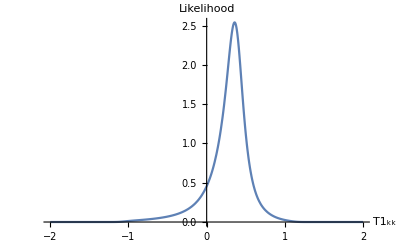

```mathematica
Plot[likelihoodT1KKinterpolation[x],{x,-2,2},PlotRange->All,AxesLabel->{Subscript[T1, kk], Likelihood}]
```

```mathematica
NMaximize[{likelihoodT1KKinterpolation[x],0.270<=x<=0.500},{x}]
```

{2.54009,{x→0.357408}}

```mathematica
chisquareT1KK[T1KK_]:=-2Log[likelihoodT1KKinterpolation[T1KK]]+2Log[likelihoodT1KKinterpolation[0.35740820186422895]];
```

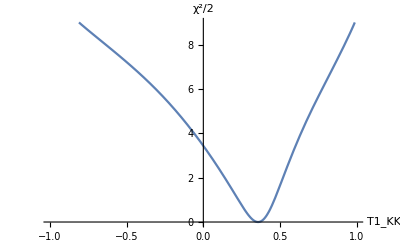

```mathematica
Plot[chisquareT1KK[x],{x,-1,1},AxesLabel->{Subscript[T1, KK],χ^2/2},PlotRange->{0,9}]
```

```mathematica
NMinimize[{chisquareT1KK[x],0.2<=x<=0.4},{x}]
```

{0.,{x→0.357408}}

```mathematica
sigmaplusT1KK=Abs[(x/.FindRoot[chisquareT1KK[x]==1,{x,0.45}])-0.35740820144920543]
```

0.106181

```mathematica
sigmaminusT1KK=Abs[(x/.FindRoot[chisquareT1KK[x]==1,{x,0.20}])-0.35740820144920543]
```

0.128703

### Profile likelihood of the absolute time T1B=T1I-ti+tb

```mathematica
(*T0B is the absolute time of arrival of the first neutrino in Baksan(corresponding to 0 time in the flux). For a point-like Earth T0B=T0I*)
(*T1B is the absolute time of detection of the first neutrino in Baksan*)
(*T1B=T0B+tb, where tb is the delay time for IMB*)
```

```mathematica
(*likelihood tb*)
```

```mathematica
profileloglikelihoodtbinterpolation=Interpolation[profileloglikelihoodtbtable]
```

InterpolatingFunction[…]

```mathematica
chisquaretb[tb_]:=profileloglikelihoodtbinterpolation[tb];
```

```mathematica
normalizationlikelihoodtb=NIntegrate[Exp[(-chisquaretb[tb])/2],{tb,0.0001,2.5}]
```

0.330726

```mathematica
likelihoodtb[tb_]:=1/normalizationlikelihoodtb Exp[(-chisquaretb[tb])/2];
```

```mathematica
(*likelihood T1B, assuming that the three time parameters are independent from each other*)
```

```mathematica
likelihoodT1Ititb[T1I_,ti_,tb_]:=likelihoodT1I[T1I]*likelihoodti[ti]*likelihoodtb[tb];
```

```mathematica
likelihoodT1B[T1B_]:=NIntegrate[likelihoodT1Ititb[T1B-tb+ti,ti,tb],{ti,0.0001,1.5},{tb,0.0001,2.5}];
```

```mathematica
likelihoodT1Btable=Table[{x,likelihoodT1B[x]},{x,-2,2.5,0.01}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{{-2.,6.09435×10^-74},{-1.99,2.04138×10^-72},{-1.98,6.5731×10^-71},{-1.97,2.03458×10^-69},{-1.96,6.05403×10^-68},{-1.95,1.73174×10^-66},{-1.94,4.76206×10^-65},{-1.93,1.2589×10^-63},{-1.92,3.19942×10^-62},{-1.91,7.81715×10^-61},{-1.9,1.83623×10^-59},{-1.89,4.14679×10^-58},{-1.88,9.00355×10^-57},{-1.87,1.87948×10^-55},{-1.86,3.77218×10^-54},{-1.85,7.27924×10^-53},{-1.84,1.3506×10^-51},{-1.83,2.40947×10^-50},{-1.82,4.13314×10^-49},{-1.81,6.8173×10^-48},{-1.8,1.08125×10^-46},{-1.79,1.64904×10^-45},{-1.78,2.41845×10^-44},{-1.77,3.4108×10^-43},{-1.76,4.6259×10^-42},{-1.75,6.0335×10^-41},{-1.74,7.5681×10^-40},{-1.73,9.12977×10^-39},{-1.72,1.05925×10^-37},{-1.71,1.18201×10^-36},{-1.7,1.26862×10^-35},{-1.69,1.30963×10^-34},{-1.68,1.30043×10^-33},{-1.67,1.2421×10^-32},{-1.66,1.14123×10^-31},{-1.65,1.00868×10^-30},{-1.64,8.5765×10^-30},{-1.63,7.01553×10^-29},{-1.62,5.52105×10^-28},{-1.61,4.18032×10^-27},{-1.6,3.04538×10^-26},{-1.59,2.13471×10^-25},{-1.58,1.43985×10^-24},{-1.57,9.34535×10^-24},{-1.56,5.8371×10^-23},{-1.55,3.50867×10^-22},{-1.54,2.0298×10^-21},{-1.53,1.13019×10^-20},{-1.52,6.05705×10^-20},{-1.51,3.1247×10^-19},{-1.5,1.55173×10^-18},{-1.49,7.41851×10^-18},{-1.48,3.41456×10^-17},{-1.47,1.51321×10^-16},{-1.46,6.45718×10^-16},{-1.45,2.65337×10^-15},{-1.44,1.05003×10^-14},{-1.43,4.00206×10^-14},{-1.42,1.46922×10^-13},{-1.41,5.19581×10^-13},{-1.4,1.77021×10^-12},{-1.39,5.81092×10^-12},{-1.38,1.83808×10^-11},{-1.37,5.60322×10^-11},{-1.36,1.64633×10^-10},{-1.35,4.66303×10^-10},{-1.34,1.27336×10^-9},{-1.33,3.35304×10^-9},{-1.32,8.51542×10^-9},{-1.31,2.08611×10^-8},{-1.3,4.93084×10^-8},{-1.29,1.12475×10^-7},{-1.28,2.47656×10^-7},{-1.27,5.26527×10^-7},{-1.26,1.08118×10^-6},{-1.25,2.14498×10^-6},{-1.24,4.11298×10^-6},{-1.23,7.62552×10^-6},{-1.22,0.0000136759},{-1.21,0.000023737},{-1.2,0.0000398948},{-1.19,0.0000649665},{-1.18,0.000102573},{-1.17,0.000157131},{-1.16,0.00023374},{-1.15,0.000337933},{-1.14,0.000475312},{-1.13,0.000651085},{-1.12,0.000869578},{-1.11,0.00113378},{-1.1,0.00144502},{-1.09,0.00180281},{-1.08,0.0022049},{-1.07,0.00264753},{-1.06,0.00312587},{-1.05,0.00363445},{-1.04,0.00416771},{-1.03,0.00472033},{-1.02,0.00528766},{-1.01,0.00586577},{-1.,0.00645159},{-0.99,0.00704288},{-0.98,0.00763805},{-0.97,0.00823615},{-0.96,0.00883663},{-0.95,0.00943933},{-0.94,0.0100443},{-0.93,0.0106517},{-0.92,0.011262},{-0.91,0.0118756},{-0.9,0.0124929},{-0.89,0.0131145},{-0.88,0.013741},{-0.87,0.014373},{-0.86,0.0150109},{-0.85,0.0156556},{-0.84,0.0163076},{-0.83,0.0169676},{-0.82,0.0176362},{-0.81,0.0183142},{-0.8,0.0190022},{-0.79,0.0197009},{-0.78,0.0204111},{-0.77,0.0211335},{-0.76,0.0218689},{-0.75,0.0226179},{-0.74,0.0233815},{-0.73,0.0241604},{-0.72,0.0249554},{-0.71,0.0257674},{-0.7,0.0265972},{-0.69,0.0274459},{-0.68,0.0283142},{-0.67,0.0292031},{-0.66,0.0301137},{-0.65,0.031047},{-0.64,0.032004},{-0.63,0.0329858},{-0.62,0.0339937},{-0.61,0.0350288},{-0.6,0.0360924},{-0.59,0.0371858},{-0.58,0.0383104},{-0.57,0.0394676},{-0.56,0.0406591},{-0.55,0.0418863},{-0.54,0.0431509},{-0.53,0.0444548},{-0.52,0.0457998},{-0.51,0.0471879},{-0.5,0.0486212},{-0.49,0.0501018},{-0.48,0.0516321},{-0.47,0.0532146},{-0.46,0.0548518},{-0.45,0.0565465},{-0.44,0.0583017},{-0.43,0.0601203},{-0.42,0.0620056},{-0.41,0.0639612},{-0.4,0.0659905},{-0.39,0.0680976},{-0.38,0.0702865},{-0.37,0.0725615},{-0.36,0.0749273},{-0.35,0.0773886},{-0.34,0.0799507},{-0.33,0.0826191},{-0.32,0.0853994},{-0.31,0.0882979},{-0.3,0.091321},{-0.29,0.0944756},{-0.28,0.0977689},{-0.27,0.101209},{-0.26,0.104803},{-0.25,0.108561},{-0.24,0.112492},{-0.23,0.116605},{-0.22,0.12091},{-0.21,0.12542},{-0.2,0.130145},{-0.19,0.135099},{-0.18,0.140294},{-0.17,0.145746},{-0.16,0.15147},{-0.15,0.157481},{-0.14,0.163797},{-0.13,0.170437},{-0.12,0.17742},{-0.11,0.184767},{-0.1,0.192501},{-0.09,0.200645},{-0.08,0.209225},{-0.07,0.218268},{-0.06,0.227804},{-0.05,0.237863},{-0.04,0.248479},{-0.03,0.259688},{-0.02,0.271528},{-0.01,0.28404},{0.,0.297268},{0.01,0.311259},{0.02,0.326063},{0.03,0.341735},{0.04,0.358331},{0.05,0.375914},{0.06,0.39455},{0.07,0.41431},{0.08,0.43527},{0.09,0.45751},{0.1,0.481118},{0.11,0.506185},{0.12,0.532811},{0.13,0.561101},{0.14,0.591164},{0.15,0.623122},{0.16,0.657095},{0.17,0.693217},{0.18,0.731618},{0.19,0.772438},{0.2,0.815811},{0.21,0.861866},{0.22,0.910716},{0.23,0.962441},{0.24,1.01708},{0.25,1.07459},{0.26,1.13484},{0.27,1.19754},{0.28,1.26221},{0.29,1.32818},{0.3,1.39451},{0.31,1.45998},{0.32,1.52317},{0.33,1.58244},{0.34,1.63605},{0.35,1.68229},{0.36,1.71961},{0.37,1.74675},{0.38,1.76288},{0.39,1.76768},{0.4,1.76134},{0.41,1.74455},{0.42,1.7184},{0.43,1.68427},{0.44,1.6437},{0.45,1.59821},{0.46,1.54927},{0.47,1.49814},{0.48,1.44589},{0.49,1.39339},{0.5,1.34127},{0.51,1.29},{0.52,1.2399},{0.53,1.19118},{0.54,1.14398},{0.55,1.09836},{0.56,1.05436},{0.57,1.01199},{0.58,0.971221},{0.59,0.932042},{0.6,0.894418},{0.61,0.858308},{0.62,0.82367},{0.63,0.790462},{0.64,0.758635},{0.65,0.728143},{0.66,0.69894},{0.67,0.670977},{0.68,0.644209},{0.69,0.61859},{0.7,0.594073},{0.71,0.570616},{0.72,0.548175},{0.73,0.526708},{0.74,0.506173},{0.75,0.486533},{0.76,0.467747},{0.77,0.449781},{0.78,0.432596},{0.79,0.416161},{0.8,0.400441},{0.81,0.385404},{0.82,0.37102},{0.83,0.35726},{0.84,0.344095},{0.85,0.331499},{0.86,0.319446},{0.87,0.307911},{0.88,0.29687},{0.89,0.2863},{0.9,0.276181},{0.91,0.266491},{0.92,0.257211},{0.93,0.248322},{0.94,0.239805},{0.95,0.231643},{0.96,0.223821},{0.97,0.216322},{0.98,0.209131},{0.99,0.202234},{1.,0.195618},{1.01,0.189269},{1.02,0.183175},{1.03,0.177324},{1.04,0.171705},{1.05,0.166307},{1.06,0.161119},{1.07,0.156131},{1.08,0.151335},{1.09,0.14672},{1.1,0.142279},{1.11,0.138001},{1.12,0.13388},{1.13,0.129907},{1.14,0.126075},{1.15,0.122378},{1.16,0.11881},{1.17,0.115368},{1.18,0.112049},{1.19,0.108854},{1.2,0.105786},{1.21,0.102854},{1.22,0.100068},{1.23,0.0974395},{1.24,0.0949842},{1.25,0.0927156},{1.26,0.0906448},{1.27,0.0887775},{1.28,0.0871119},{1.29,0.0856379},{1.3,0.0843365},{1.31,0.0831812},{1.32,0.0821408},{1.33,0.0811825},{1.34,0.080275},{1.35,0.0793921},{1.36,0.0785139},{1.37,0.0776283},{1.38,0.0767304},{1.39,0.0758207},{1.4,0.074904},{1.41,0.0739871},{1.42,0.0730772},{1.43,0.0721806},{1.44,0.0713025},{1.45,0.0704463},{1.46,0.0696137},{1.47,0.0688052},{1.48,0.0680206},{1.49,0.0672588},{1.5,0.0665184},{1.51,0.0657981},{1.52,0.0650963},{1.53,0.0644116},{1.54,0.0637426},{1.55,0.0630883},{1.56,0.0624474},{1.57,0.061819},{1.58,0.0612024},{1.59,0.0605966},{1.6,0.060001},{1.61,0.0594151},{1.62,0.0588382},{1.63,0.05827},{1.64,0.0577098},{1.65,0.0571574},{1.66,0.0566124},{1.67,0.0560745},{1.68,0.0555434},{1.69,0.0550188},{1.7,0.0545004},{1.71,0.0539881},{1.72,0.0534816},{1.73,0.0529808},{1.74,0.0524855},{1.75,0.0519956},{1.76,0.0515108},{1.77,0.051031},{1.78,0.0505561},{1.79,0.0500861},{1.8,0.0496207},{1.81,0.0491599},{1.82,0.0487035},{1.83,0.0482515},{1.84,0.0478038},{1.85,0.0473603},{1.86,0.0469209},{1.87,0.0464855},{1.88,0.046054},{1.89,0.0456264},{1.9,0.0452026},{1.91,0.0447825},{1.92,0.0443661},{1.93,0.0439532},{1.94,0.0435439},{1.95,0.043138},{1.96,0.0427354},{1.97,0.0423362},{1.98,0.0419402},{1.99,0.0415474},{2.,0.0411577},{2.01,0.0407711},{2.02,0.0403875},{2.03,0.0400067},{2.04,0.0396288},{2.05,0.0392537},{2.06,0.0388813},{2.07,0.0385115},{2.08,0.0381444},{2.09,0.0377797},{2.1,0.0374174},{2.11,0.0370575},{2.12,0.0366998},{2.13,0.0363444},{2.14,0.0359911},{2.15,0.0356398},{2.16,0.0352904},{2.17,0.0349429},{2.18,0.0345971},{2.19,0.034253},{2.2,0.0339105},{2.21,0.0335695},{2.22,0.0332298},{2.23,0.0328914},{2.24,0.0325541},{2.25,0.0322178},{2.26,0.0318824},{2.27,0.0315477},{2.28,0.0312137},{2.29,0.0308802},{2.3,0.030547},{2.31,0.030214},{2.32,0.029881},{2.33,0.0295478},{2.34,0.0292143},{2.35,0.0288803},{2.36,0.0285455},{2.37,0.0282097},{2.38,0.0278728},{2.39,0.0275344},{2.4,0.0271944},{2.41,0.0268524},{2.42,0.0265081},{2.43,0.0261614},{2.44,0.0258117},{2.45,0.0254589},{2.46,0.0251025},{2.47,0.0247421},{2.48,0.0243774},{2.49,0.0240078},{2.5,0.023633}}

```mathematica
Export["likelihoodT1Btable.csv",likelihoodT1Btable]
```

likelihoodT1Btable.csv

```mathematica
likelihoodT1Binterpolation=Interpolation[likelihoodT1Btable]
```

InterpolatingFunction[…]

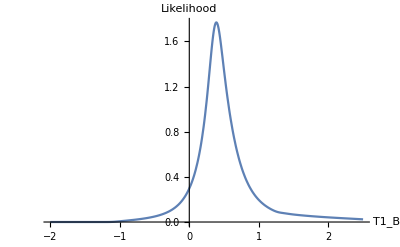

```mathematica
Plot[likelihoodT1Binterpolation[x],{x,-2,2.5},PlotRange->All,AxesLabel->{Subscript[T1, B], Likelihood}]
```

```mathematica
NMaximize[{likelihoodT1Binterpolation[x],0.1<=x<=0.400},{x}]
```

{1.76771,{x→0.389278}}

```mathematica
chisquareT1B[T1B_]:=-2Log[likelihoodT1Binterpolation[T1B]]+2Log[likelihoodT1Binterpolation[0.3892821326220788]];
```

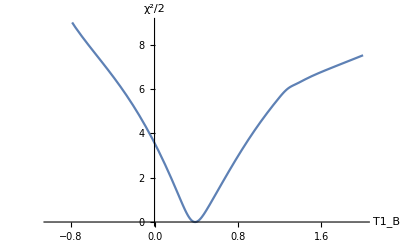

```mathematica
Plot[chisquareT1B[x],{x,-1,2},AxesLabel->{Subscript[T1, B],χ^2/2},PlotRange->{0,9}]
```

```mathematica
NMinimize[{chisquareT1B[x],0.3<=x<=0.5},{x}]
```

{-1.12933×10^-9,{x→0.389278}}

```mathematica
sigmaplusT1B=Abs[(x/.FindRoot[chisquareT1B[x]==1,{x,0.6}])-0.3892821326220788]
```

0.166626

```mathematica
sigmaminusT1B=Abs[(x/.FindRoot[chisquareT1B[x]==1,{x,0.20}])-0.3892821326220788]
```

0.139694